# EM fields of moving charges

## Poruri Sai Rahul :: PH09B011

```mathematica
-
```

```mathematica
Remove["Global`*"]
```

```mathematica
w[t_] = √((c^2/g)^2+(c*t)^2)
```

√(c^4/g^2+c^2 t^2)

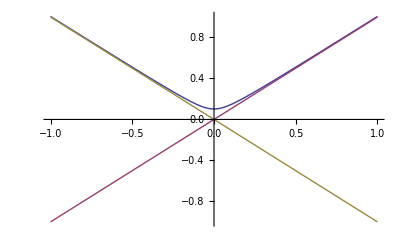

```mathematica
Plot[{w[t]/.{c->1,g->9.8},c*t/.{c->1},-c*t/.{c->1}},{t,-1,1},PlotRange->Full]
```

```mathematica
v[t_]=D[w[t],t]
```

(c^2 t)/(√(c^4/g^2+c^2 t^2))

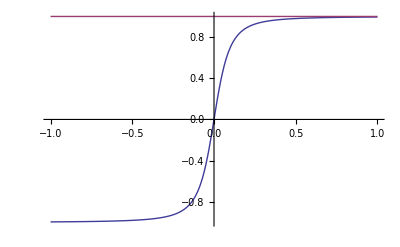

```mathematica
Plot[{v[t]/.{c->1,g->9.8},c/.{c->1}},{t,-1,1}]
```

```mathematica
a[t_] =D[v[t],t]
```

-(c^4 t^2)/((c^4/g^2+c^2 t^2)^(3/2))+c^2/(√(c^4/g^2+c^2 t^2))

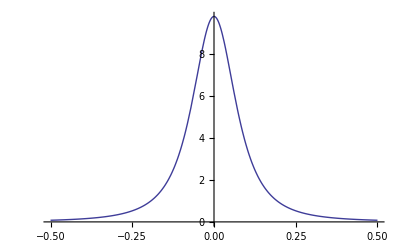

```mathematica
Plot[a[t]/.{c->1,g->9.8},{t,-.5,.5}]
```

## First level section heading

Text lorem ipsum dolor sit amet, consectetuer adipiscing elit, sed diam nonummy nibh euismod tincidunt ut laoreet dolore magna aliquam erat volutpat. Ut wisi enim ad minim veniam, quis nostrud exerci tation ullamcorper suscipit lobortis nisl ut aliquip ex ea commodo consequat.

Item duis autem vel eum iriure dolor in hendrerit in vulputate velit esse molestie consequat, vel illum dolore eu feugiat nulla facilisis at vero eros et accumsan et iusto odio dignissim qui blandit praesent luptatum zril delenit augue duis dolore te feugait nulla facilisi.

Subitem nam liber tempor cum soluta nobis eleifend option congue nihil imperdiet doming id quod mazim placerat facer possim assum.

Subitem typi non habent claritatem insitam; est usus legentis in is qui facit eorum claritatem.

### Second level section heading

Text duis autem vel eum iriure dolor in hendrerit in vulputate velit esse molestie consequat, vel illum dolore eu feugiat nulla facilisis at vero eros et accumsan et iusto odio dignissim qui blandit praesent luptatum zril delenit augue duis dolore te feugait nulla facilisi.

### Second level section heading

Text lorem ipsum dolor sit amet, consectetuer adipiscing elit, sed diam nonummy nibh euismod tincidunt ut laoreet dolore magna aliquam erat volutpat. Ut wisi enim ad minim veniam, quis nostrud exerci tation ullamcorper suscipit lobortis nisl ut aliquip ex ea commodo consequat.

#### Third level section heading

```mathematica
Plot[Evaluate[Table[BesselJ[n,x],{n,4}]],{x,0,10},Filling->Axis]
```

-Graphics-

### Second level section heading

-Graphics- | SideCaption duis autem vel eum iriure dolor in hendrerit in vulputate velit esse molestie consequat, vel illum dolore eu feugiat nulla facilisis at vero eros et accumsan et iusto odio dignissim qui blandit praesent luptatum zril delenit augue duis dolore te feugait nulla facilisi.